```mathematica
SetDirectory["D:\\program files\\Wolfram Research\\Mathematica\\7.0\\AddOns\\ExtraPackages\\MadEvent analysis\\parameter_scans\\plots_for_pub"];
Timing[testp=Import["ax_full2.lhe","Table"];]
```

{21.60614,Null}

```mathematica
Timing[testp2=Import["grv_full2.lhe","Table"];]
```

{21.90254,Null}

```mathematica
Timing[testp3=Import["rpv_full2.lhe","Table"];]
```

{21.79334,Null}

```mathematica
Timing[eventListp=ReadME[testp]; ]
```

{0.2028,Null}

```mathematica
Timing[eventListp2=ReadME[testp2]; ]
```

{0.2028,Null}

```mathematica
Timing[eventListp3=ReadME[testp3]; ]
```

{0.1872,Null}

```mathematica
Nev = Length[eventListp]
```

10000

```mathematica
Nev2 = Length[eventListp2]
```

10000

```mathematica
Nev3 = Length[eventListp3]
```

10000

```mathematica
tsp={eventListp[[1]],eventListp3[[2]]};


EventPrint /@ %;
```

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
u | in | 0 | 0 | 501 | 0 | 0. | 0. | 146.307 | 146.307 | 0. | 0. | 1.
uBar | in | 0 | 0 | 0 | 501 | 0. | 0. | -2075.1 | 2075.1 | 0. | 0. | -1.
(χ̃)_0 | decayed | 1 | 2 | 0 | 0 | -191.024 | -36.1949 | -633.486 | 823.382 | 488.726 | 0. | 1.
(χ̃)_0 | decayed | 1 | 2 | 0 | 0 | 191.024 | 36.1949 | -1295.3 | 1398.02 | 488.726 | 0. | -1.
particle[9000006] | out | 3 | 3 | 0 | 0 | 50.173 | -115.48 | -60.1369 | 139.533 | 0. | 0. | 1.
d | out | 3 | 3 | 502 | 0 | -216.211 | 11.6589 | -572.143 | 611.744 | 0. | 0. | -1.
dBar | out | 3 | 3 | 0 | 502 | -24.9861 | 67.6267 | -1.2063 | 72.105 | 0. | 0. | 1.
particle[9000006] | out | 4 | 4 | 0 | 0 | 63.1913 | -93.0094 | -561.948 | 573.087 | 0. | 0. | 1.
d | out | 4 | 4 | 503 | 0 | 179.232 | 209.373 | -607.617 | 667.203 | 0. | 0. | 1.
dBar | out | 4 | 4 | 0 | 503 | -51.3995 | -80.169 | -125.739 | 157.732 | 0. | 0. | -1.)

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
c | in | 0 | 0 | 501 | 0 | 0. | 0. | 973.877 | 973.877 | 0. | 0. | 1.
cBar | in | 0 | 0 | 0 | 501 | 0. | 0. | -586.876 | 586.876 | 0. | 0. | -1.
(χ̃)_0 | decayed | 1 | 2 | 0 | 0 | 351.383 | -394.256 | 432.89 | 839.735 | 488.726 | 0. | -1.
(χ̃)_0 | decayed | 1 | 2 | 0 | 0 | -351.383 | 394.256 | -45.8894 | 721.018 | 488.726 | 0. | 1.
(⋁_μ)^c | out | 3 | 3 | 0 | 0 | -90.4239 | -114.79 | 29.8928 | 149.153 | 0. | 0. | -1.
s | out | 3 | 3 | 502 | 0 | 95.88 | -164.607 | 92.5099 | 211.77 | 0. | 0. | -1.
dBar | out | 3 | 3 | 0 | 502 | 345.927 | -114.859 | 310.487 | 478.811 | 0. | 0. | -1.
(⋁_e)^c | out | 4 | 4 | 0 | 0 | -44.8739 | -7.10066 | 11.7283 | 46.9216 | 0. | 0. | -1.
s | out | 4 | 4 | 503 | 0 | -270.371 | 494.21 | -9.41701 | 563.412 | 0. | 0. | -1.
sBar | out | 4 | 4 | 0 | 503 | -36.1381 | -92.8535 | -48.2008 | 110.684 | 0. | 0. | -1.)

```mathematica
eventListOutLp=SetOut[eventListp];
```

```mathematica
eventListOutLp2=SetOut[eventListp2];
```

```mathematica
eventListOutLp3=SetOut[eventListp3];
```

```mathematica
{eventListOutLp[[1]],eventListOutLp2[[24]]};
EventPrint /@ %;
```

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
particle[9000006] | out | 3 | 3 | 0 | 0 | 50.173 | -115.48 | -60.1369 | 139.533 | 0. | 0. | 1.
d | out | 3 | 3 | 502 | 0 | -216.211 | 11.6589 | -572.143 | 611.744 | 0. | 0. | -1.
dBar | out | 3 | 3 | 0 | 502 | -24.9861 | 67.6267 | -1.2063 | 72.105 | 0. | 0. | 1.
particle[9000006] | out | 4 | 4 | 0 | 0 | 63.1913 | -93.0094 | -561.948 | 573.087 | 0. | 0. | 1.
d | out | 4 | 4 | 503 | 0 | 179.232 | 209.373 | -607.617 | 667.203 | 0. | 0. | 1.
dBar | out | 4 | 4 | 0 | 503 | -51.3995 | -80.169 | -125.739 | 157.732 | 0. | 0. | -1.)

(pid | in/out | mother1 | mother2 | color1 | color2 | px | py | pz | p0 | mass | 6 | hel
particle[1000049] | out | 3 | 3 | 0 | 0 | 104.165 | -46.018 | 193.956 | 224.916 | 0. | 0. | -1.
c | out | 3 | 3 | 502 | 0 | -78.6816 | -107.211 | 59.728 | 145.782 | 0. | 0. | 1.
cBar | out | 3 | 3 | 0 | 502 | -207.575 | -608.469 | 345.539 | 729.876 | 0. | 0. | -1.
particle[1000049] | out | 4 | 4 | 0 | 0 | 302.072 | 315.007 | 260.789 | 508.417 | 0. | 0. | -1.
s | out | 4 | 4 | 503 | 0 | -13.464 | 1.19472 | 12.6858 | 18.5375 | 0. | 0. | 1.
sBar | out | 4 | 4 | 0 | 503 | -106.517 | 445.497 | 492.584 | 672.646 | 0. | 0. | -1.)

```mathematica
JustTheDM={9000006,_,_,_,_,_,_,_,_,_,_,_,_} |{1000049,_,_,_,_,_,_,_,_,_,_,_,_}|{12,_,_,_,_,_,_,_,_,_,_,_,_}|{14,_,_,_,_,_,_,_,_,_,_,_,_}|{16,_,_,_,_,_,_,_,_,_,_,_,_}|{-12,_,_,_,_,_,_,_,_,_,_,_,_}|{-14,_,_,_,_,_,_,_,_,_,_,_,_}|{-16,_,_,_,_,_,_,_,_,_,_,_,_};
RemoveDM[event_]:=(DeleteCases[event,JustTheDM,{2}]);
eventListOutJets= RemoveDM[eventListOutLp];
eventListOutJets2= RemoveDM[eventListOutLp2];
eventListOutJets3= RemoveDM[eventListOutLp3];
```

```mathematica
JetCuts[event_]:=If[ptOf[event]>40,event];
eventListOutCutJets=Map[JetCuts,eventListOutJets,{2}];
eventListOutCutJets=DeleteCases[eventListOutCutJets,Null,2];
eventListOutCutJets2=Map[JetCuts,eventListOutJets2,{2}];
eventListOutCutJets2=DeleteCases[eventListOutCutJets2,Null,2];
eventListOutCutJets3=Map[JetCuts,eventListOutJets3,{2}];
eventListOutCutJets3=DeleteCases[eventListOutCutJets3,Null,2];
```

```mathematica
EtaCuts[event_]:=If[etaOf[event]<2.5,event];
eventListOutCut=Map[EtaCuts,eventListOutCutJets,{2}];
eventListOutCut=DeleteCases[eventListOutCut,Null,2];
eventListOutCut2=Map[EtaCuts,eventListOutCutJets2,{2}];
eventListOutCut2=DeleteCases[eventListOutCut2,Null,2];
eventListOutCut3=Map[EtaCuts,eventListOutCutJets3,{2}];
eventListOutCut3=DeleteCases[eventListOutCut3,Null,2];
```

```mathematica
weightListAx=Map[5.4*((0.107470*10^-19)/(1.11*10^-16))^2&,eventListOutLp[[1;;Nev]]];
weightListGrv=Map[5.4*((0.93538*10^-20)/(1.066*10^-15))^2&,eventListOutLp2[[1;;Nev2]]];
weightListRPV=Map[5.4*((0.10368*10^-19)/(2.275*10^-16))^2&,eventListOutLp3[[1;;Nev3]]];
```

```mathematica
ptmiss[event_]:=ptOf[event[[1]]]+ptOf[event[[4]]];
metAxPlot = Map[ptmiss[#] &, eventListOutLp[[1;;Nev]]];
metGrvPlot = Map[ptmiss[#] &, eventListOutLp2[[1;;Nev2]]];
metRPVPlot= Map[ptmiss[#] &, eventListOutLp3[[1;;Nev3]]];
```

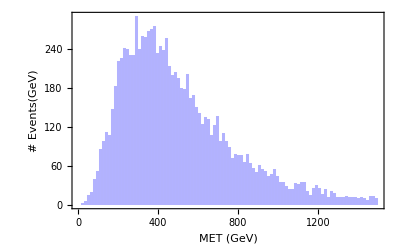

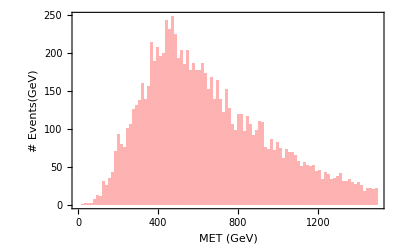

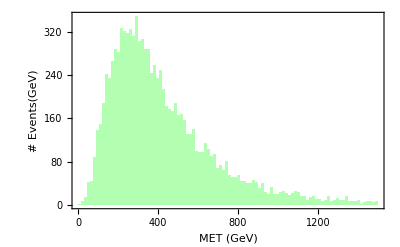

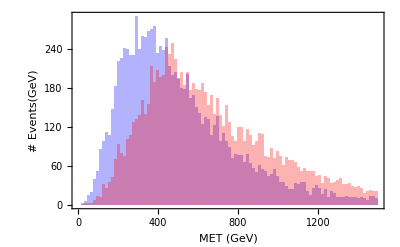

```mathematica
g1=Histogram[metAxPlot, {0,1500,15},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"MET (GeV)","# Events(GeV)"}]
g2=Histogram[metGrvPlot, {0,1500,15},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"MET (GeV)","# Events(GeV)"}]
g3=Histogram[metRPVPlot, {0,1500,15},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"MET (GeV)","# Events(GeV)"}]
Show[g1,g2]
```

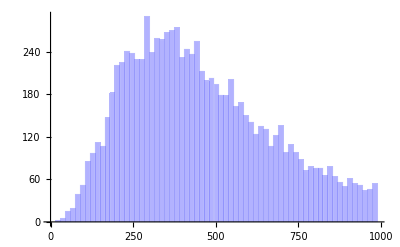

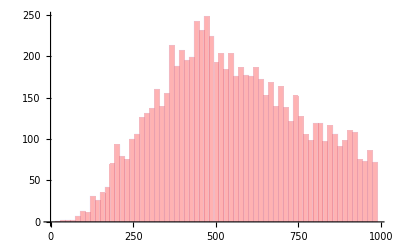

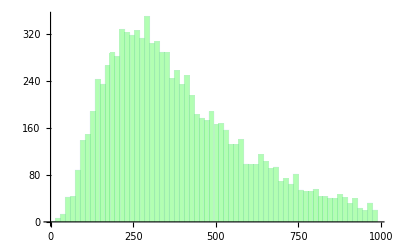

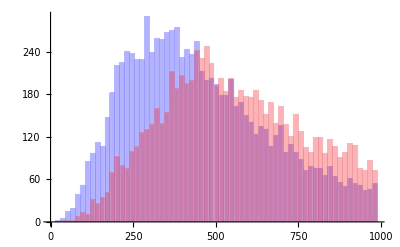

```mathematica
g1=Histogram[metAxPlot, {0,1000,15},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g2=Histogram[metGrvPlot, {0,1000,15},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g3=Histogram[metRPVPlot, {0,1000,15},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
Show[g1,g2]
```

```mathematica
MHT[event_]:=Abs[√((-Total[Map[pxOf,event,{1}]])^2+(-Total[Map[pxOf,event,{1}]])^2)];
```

```mathematica
MHTAxPlot = Map[MHT[#] &, eventListOutCut[[1;;Nev]]];
MHTGrvPlot = Map[MHT[#] &, eventListOutCut2[[1;;Nev2]]];
MHTRPVPlot = Map[MHT[#] &, eventListOutCut3[[1;;Nev3]]];
```

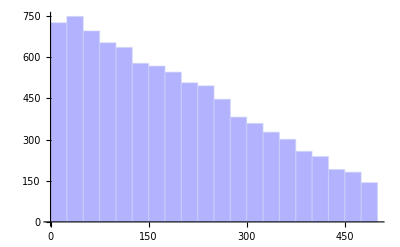

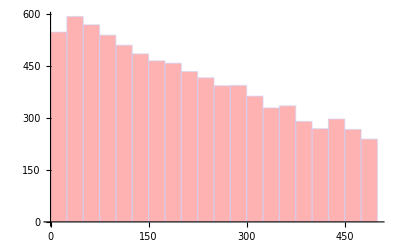

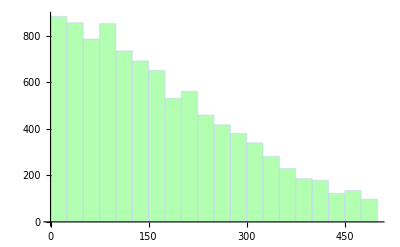

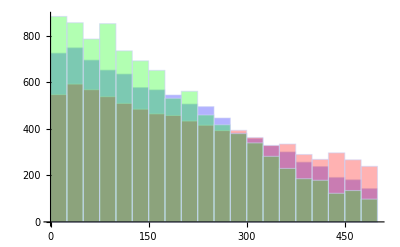

```mathematica
h1=Histogram[MHTAxPlot, {0,500,25},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
h2=Histogram[MHTGrvPlot, {0,500,25},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]

h3=Histogram[MHTRPVPlot, {0,500,25},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
Show[h1,h2,h3]
```

```mathematica
JetInvMass[event_] := Sqrt[2*(enOf[event[[3]]]*enOf[event[[4]]]-ThreeVectorFrom[event[[3]]].ThreeVectorFrom[event[[4]]])];
JetInvMassAxPlot = Map[JetInvMass[#] &, eventListOutLp[[1;;Nev]]];
JetInvMassGrvPlot = Map[JetInvMass[#] &, eventListOutLp2[[1;;Nev2]]];
JetInvMassRPVlot = Map[JetInvMass[#] &, eventListOutLp3[[1;;Nev3]]];
```

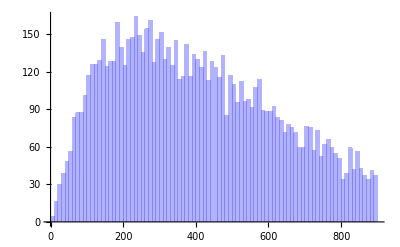

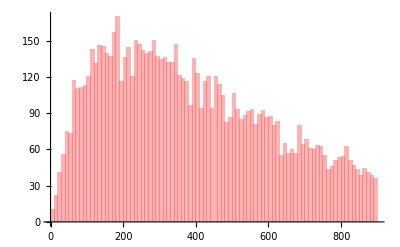

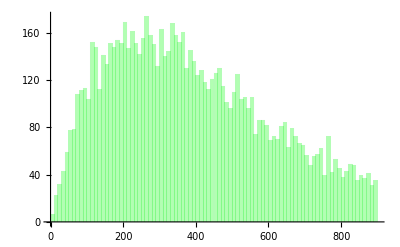

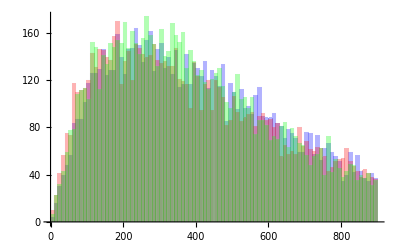

```mathematica
g1=Histogram[JetInvMassAxPlot , {0,900,10},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g2=Histogram[JetInvMassGrvPlot, {0,900,10},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g3=Histogram[JetInvMassRPVlot, {0,900,10},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]

Show[g1,g2,g3]
```

```mathematica
numJets[event_]:=Length[event];
numJetsAxPlot = Map[numJets[#] &, eventListOutCut[[1;;Nev]]];
numJetsGrvPlot = Map[numJets[#] &, eventListOutCut2[[1;;Nev2]]];
numJetsRPVPlot = Map[numJets[#] &, eventListOutCut3[[1;;Nev3]]];
```

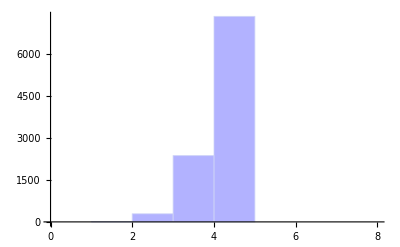

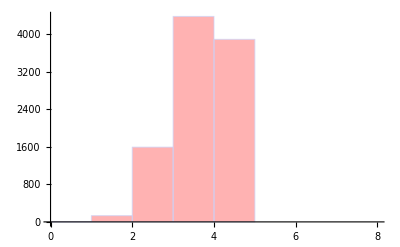

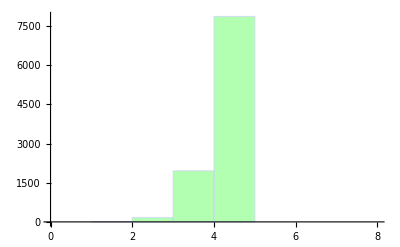

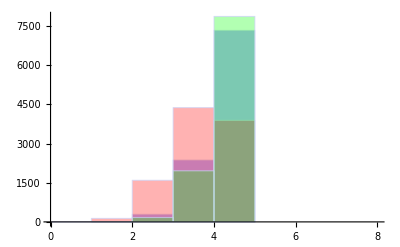

```mathematica
g1=Histogram[numJetsAxPlot, {0,8,1},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g2=Histogram[numJetsGrvPlot, {0,8,1},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g3=Histogram[numJetsRPVPlot, {0,8,1},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]

Show[g1,g2,g3]
```

```mathematica
JetPtTot[event_]:=Total[Map[ptOf[#]&, event],2]
JetPtTotAxPlot = Map[JetPtTot[#] &, eventListOutCut[[1;;Nev]]];
JetPtTotGrvPlot = Map[JetPtTot[#] &, eventListOutCut2[[1;;Nev2]]];
JetPtTotRPVPlot = Map[JetPtTot[#] &, eventListOutCut3[[1;;Nev3]]];
```

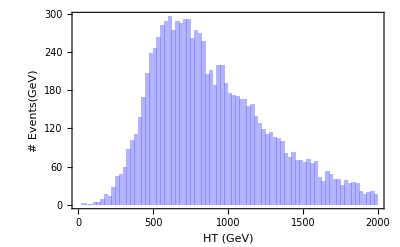

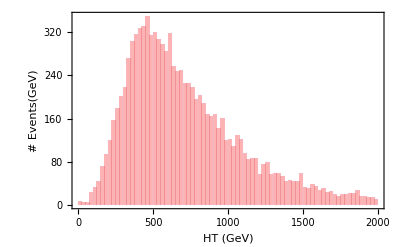

```mathematica
g1=Histogram[JetPtTotAxPlot, {0,2000,25},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"HT (GeV)","# Events(GeV)"}]
g2=Histogram[JetPtTotGrvPlot, {0,2000,25},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"HT (GeV)","# Events(GeV)"}]
g3=Histogram[JetPtTotRPVPlot, {0,2000,25},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"HT (GeV)","# Events(GeV)"}]
Show[g1,g2]
```

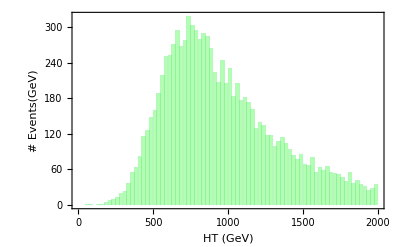

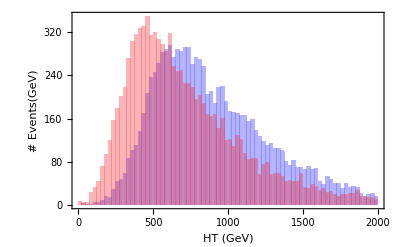

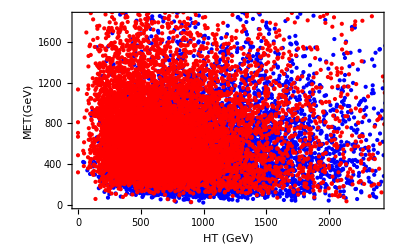

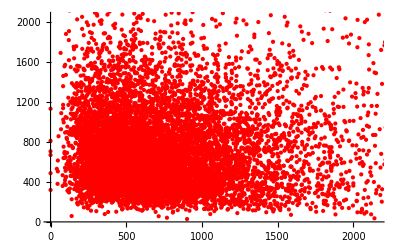

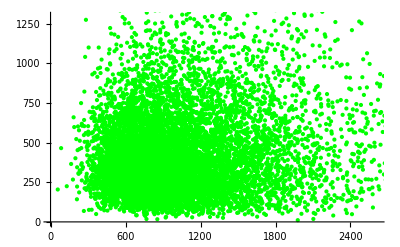

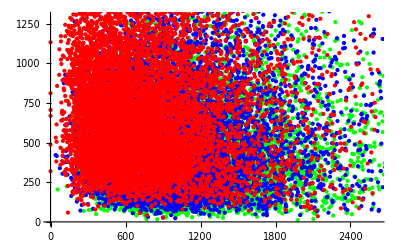

```mathematica
HtvsMETAxdata=Transpose@{JetPtTotAxPlot,metAxPlot};
HtvsMETGrvdata=Transpose@{JetPtTotGrvPlot,metGrvPlot};
HtvsMETRPVdata=Transpose@{JetPtTotRPVPlot,metRPVPlot};
SetOptions[ListPlot,BaseStyle->{FontFamily->"Times",FontSize->20}];
g1=ListPlot[{HtvsMETAxdata,HtvsMETGrvdata},PlotStyle->{Blue,Red},ImageSize->Scaled[.4],Frame->True,FrameLabel->{"HT (GeV)","MET(GeV)"}]
g2=ListPlot[HtvsMETGrvdata,PlotStyle->Red]
g3 =ListPlot[HtvsMETRPVdata,PlotStyle->Green]
Show[g3,g1]
```

```mathematica
JetInvMassTot[event_]:=Sqrt[(Total[Map[enOf[#]&,event],2]*Total[Map[enOf[#]&,event],2])-((Total[Map[ThreeVectorFrom[#]&,event],2])  (Total[Map[ThreeVectorFrom[#]&,event],2]))];
JetInvMassTotAxPlot = Map[JetInvMassTot[#] &, eventListOutCut[[1;;Nev]]];
JetInvMassTotGrvPlot = Map[JetInvMassTot[#] &, eventListOutCut2[[1;;Nev2]]];
JetInvMassTotRPVPlot = Map[JetInvMassTot[#] &, eventListOutCut3[[1;;Nev3]]];
```

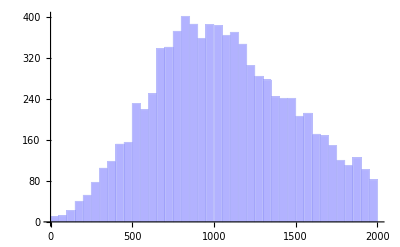

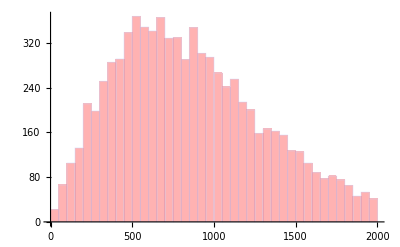

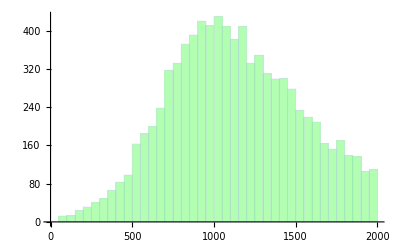

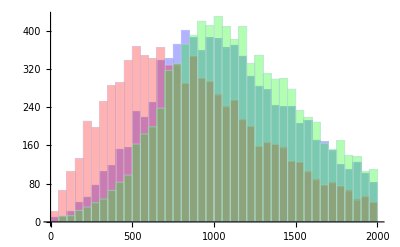

```mathematica
g1=Histogram[JetInvMassTotAxPlot, {0,2000,50},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g2=Histogram[JetInvMassTotGrvPlot, {0,2000,50},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g3=Histogram[JetInvMassTotRPVPlot, {0,2000,50},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]

Show[g1,g2,g3]
```

```mathematica
LeadingEta[event_]:=etaOf[First[PTSort[event]]];
LeadingEtaAxPlot = Map[LeadingEta[#] &, eventListOutCut[[1;;Nev]]];
LeadingEtaGrvPlot = Map[LeadingEta[#] &, eventListOutCut2[[1;;Nev2]]];
{{LeadingEtaRPVPlot = Map[LeadingEta[#] &, eventListOutCut3[[1;;Nev3]]];}, {□}}
```

First::first: {} has a length of zero and no first element.

General::stop: Further output of First :: first will be suppressed during this calculation.

{{Null},{□}}

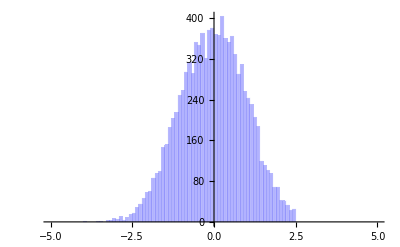

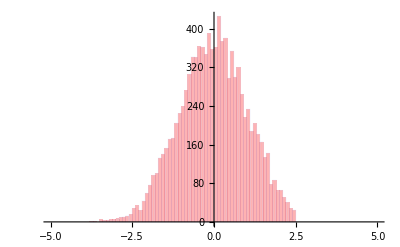

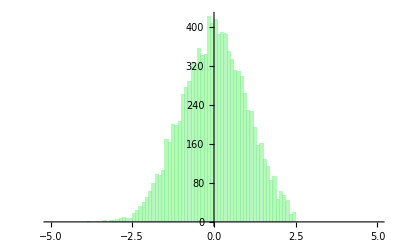

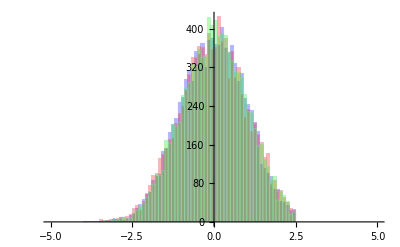

```mathematica
g1=Histogram[LeadingEtaAxPlot, {-5,5,0.1},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g2=Histogram[LeadingEtaGrvPlot, {-5,5,0.1},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g3=Histogram[LeadingEtaRPVPlot, {-5,5,0.1},ChartStyle->{Directive[Green,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]

Show[g1,g2,g3]
```

```mathematica
LeadingJet[event_]:=ptOf[First[PTSort[event]]];
LeadingJetAxPlot = Map[LeadingJet[#] &, eventListOutCut[[1;;Nev]]];
LeadingJetGrvPlot = Map[LeadingJet[#] &, eventListOutCut2[[1;;Nev2]]];
LeadingJetRPVPlot= Map[LeadingJet[#] &, eventListOutCut3[[1;;Nev3]]];
```

First::first: {} has a length of zero and no first element.

General::stop: Further output of First :: first will be suppressed during this calculation.

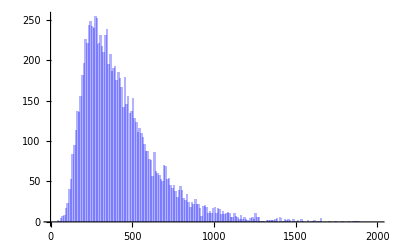

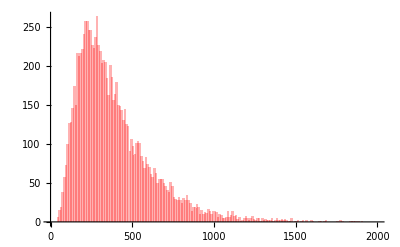

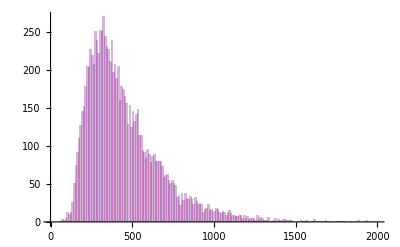

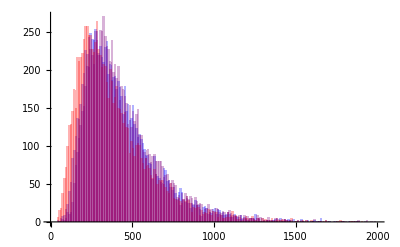

```mathematica
g1=Histogram[LeadingJetAxPlot, {0,2000,10},ChartStyle->{Directive[Blue,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g2=Histogram[LeadingJetGrvPlot, {0,2000,10},ChartStyle->{Directive[Red,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
g3=Histogram[LeadingJetRPVPlot, {0,2000,10},ChartStyle->{Directive[Purple,Opacity[.3]]},BaseStyle->{FontWeight->"Bold",FontSize->18},Axes->True,AxesOrigin->{0,0}]
Show[g1,g2,g3]
```